```mathematica
coord = {t,r,θ,ϕ};
metric=DiagonalMatrix[{α[r],-β[r],-r^2,-r^2 Sin[θ]^2}];
Get["C:\\Users\\Gianmarco\\Downloads\\diffgeo.m"]
```

ds2 = -r^2 dd[θ]^2-r^2 dd[ϕ]^2 Sin[θ]^2+dd[t]^2 α[r]-dd[r]^2 β[r]

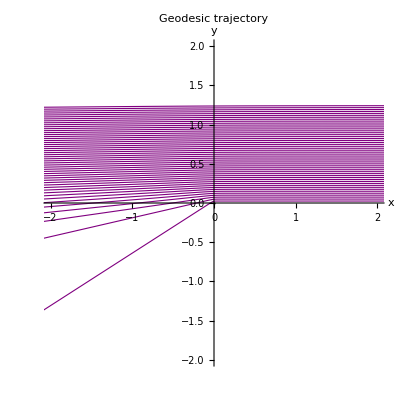

```mathematica
Einstein;
dsol=DSolve[{Einstein[[1,1]]==0 && Einstein[[2,2]]==0},{α[r],β[r]},r];
Simplify[Einstein /.D[dsol,r] /. D[dsol,{r,2}] /.dsol];
metricschw=ArrayReshape[metric/.dsol/. Exp[C[1]]->-R /. C[2]-> 1,{4,4}];
L=Sqrt[({t'[s],r'[s],θ'[s],ϕ'[s]} . (metricschw/.r->r[s]/.θ->θ[s]/.ϕ->ϕ[s]/.R->1/200)). {t'[s],r'[s],θ'[s],ϕ'[s]}];
masslesscondeq=Simplify[Solve[L^2==0,t'[s]]][[2]];
Lagrangeeqs=Simplify[Table[D[D[L^2,v'[s]],s]- D[L^2,v[s]],{v,{r,θ,ϕ}}]/. D[masslesscondeq,s]/. masslesscondeq];
eq1=Simplify[Lagrangeeqs[[1]]/. θ[s] ->π/2 /.θ'[s] ->0 /.θ''[s] ->0 ];
eq2 =Simplify[Lagrangeeqs[[3]]/. θ[s] ->π/2 /.θ'[s] ->0 /.θ''[s] ->0 ];
geodesics[a_?NumericQ]:=NDSolve[{eq1==0 &&eq2==0 , {r[0]== D,ϕ[0]==a/D,r'[0]==-D[D, D],ϕ'[0]==-D[a/D, D]}}/.D->10,{r[s],ϕ[s]},{s,0,30}];
fix=InterpolatingFunction[a_,b___]:>If[s>a[[1,2]],0,InterpolatingFunction[a,b]];
rsol[s_]=Quiet[Table[r[s]/.geodesics[i/40][[1]]/.fix,{i,1,50,1}]];
ϕsol[s_]=Quiet[Table[ϕ[s]/.geodesics[i/40][[1]]/.fix,{i,1,50,1}]];
y[s_]=rsol[s]*Sin[ϕsol[s]];
x[s_]=rsol[s]*Cos[ϕsol[s]];

p=Quiet[Table[ParametricPlot[{x[s][[i]],y[s][[i]]},{s,0,30},PlotRange->{{-2,2},{-2,2}},PlotStyle->Directive[Thickness[0.002],{Purple}],PlotLabel->"Geodesic trajectory",AxesLabel->{"x","y"}],{i,1,50,1}]];
Show[p,Graphics[{Thick,Circle[{0,0},1/200]}]]
```

{4.563,1.66212,0.124696}

{{r[s]→InterpolatingFunction[…][s],θ[s]→InterpolatingFunction[…][s],ϕ[s]→InterpolatingFunction[…][s]}}

{0.,6.05265}

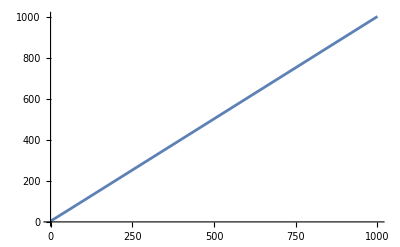

```mathematica
sl={r->Sqrt[x^2+y^2+z^2],θ->ArcTan[z/Sqrt[x^2+y^2+z^2],Sqrt[x^2+y^2]/Sqrt[x^2+y^2+z^2]],ϕ->ArcTan[x/Sqrt[x^2+y^2],y/Sqrt[x^2+y^2]]};
x0=l-Cos[α]*Sin[τ]*ϵ;
y0=a+Sin[α]*Sin[τ]*ϵ;
z0=ϵ*Cos[τ];
initial[ϵ_]:={r,θ,ϕ} /.sl /.x->x0/.y->y0/.z->z0;
N[initial[0]/.l->5/.α->1/.τ->2/.a->-1/5/.ϵ->1]
sol[α0_,τ0_]:=NDSolve[{Lagrangeeqs[[1]]==0,Lagrangeeqs[[2]]==0,Lagrangeeqs[[3]]==0,r[0]==initial[0][[1]],θ[0]==initial[0][[2]],ϕ[0]==initial[0][[3]],r'[0]==D[initial[0][[1]],ϵ],θ'[0]==D[initial[0][[2]],ϵ],ϕ'[0]==D[initial[0][[3]],ϵ]}/. {l->5,a->-1/5,α->α0,τ->τ0,ϵ->1}//Evaluate,{r[s],θ[s],ϕ[s]},{s,0,1000}];
soluzione=sol[2,π/2]
rsol=r[s]/.soluzione[[1]];
rsol/.s->1 //Timing
Plot[rsol,{s,0,1000}]
```

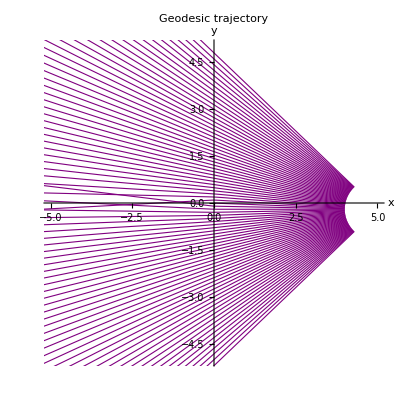

```mathematica
fix=InterpolatingFunction[a_,b___]:>If[s>a[[1,2]],0,InterpolatingFunction[a,b]];
rsol2[s_]=Quiet[Table[r[s]/.sol[π*i/160,π/2][[1]]/.fix,{i,-40,40,1}]];
ϕsol2[s_]=Quiet[Table[ϕ[s]/.sol[π*i/160,π/2][[1]]/.fix,{i,-40,40,1}]];
y2[s_]=rsol2[s]*Sin[ϕsol2[s]];
x2[s_]=rsol2[s]*Cos[ϕsol2[s]];

p=Quiet[Table[ParametricPlot[{x2[s][[i]],y2[s][[i]]},{s,0,100},PlotRange->{{-5,5},{-5,5}},PlotStyle->Directive[Thickness[0.002],{Purple}],PlotLabel->"Geodesic trajectory",AxesLabel->{"x","y"}],{i,1,81,1}]];
Show[p,Graphics[{Thick,Circle[{0,0},1/200]}]]
```

```mathematica
dim=512;
solutions=Quiet[Table[sol[π/16*(i-dim/2)/dim,π/2-π/16*(j-dim/2)/dim]/.fix,{i,1,dim,1},{j,1,dim,1}]];
asymptoticXY=Table[( rinf=r[s]/. solutions[[i,j]]/. s->100;
If[rinf[[1]]>0,{π-Mod[ϕ[s],2π],π/2-θ[s]}/.solutions[[i,j]]/. s->1000,{0,0}]),{i,1,dim,1},{j,1,dim,1}];
xy2XY=Table[asymptoticXY[[i,j]]*dim/(π/16)+dim/2,{i,dim},{j,dim}];
XY=Round[xy2XY];
```

```mathematica
XY
```

```mathematica
im=Import["C:\\Users\\Gianmarco\\Downloads\\im.jpeg"];
img=ImageResize[im,{dim=512,dim}]
```

-Graphics-

```mathematica
imd=ImageData[img];
Dimensions[imd]
data=Table[
If[XY⟦i,j,1,1⟧≥1&&XY⟦i,j,1,2⟧≥1&&XY⟦i,j,1,1⟧≤dim&&XY⟦i,j,1,2⟧≤dim,imd⟦XY⟦i,j,1,1⟧,XY⟦i,j,1,2⟧⟧,{0,0,0}],{i,dim},{j,dim}];
isListOfThreeNumbersQ[element_]:=MatchQ[element,{_?NumberQ,_?NumberQ,_?NumberQ}];

(*Replace elements that are not lists of three numbers*)
processeddata=Map[If[isListOfThreeNumbersQ[#],#,{0,0,0}]&,data,{2}];

(*Output the processed matrix*)
Image[processeddata]
```

{64,64,3}

-Graphics-